# Evolución temporal función de onda

### Parámetros del problema

```mathematica
Δt = 0.005;
a = -100;
b = 100;
n = 2000;
Δx = (b-a)/n;
Δk = (2π)/(b-a);
k0 = N[-π/Δx];
ℏ = 1;
m = 2;
L = ℏ/(√(2m));
V0 = 0.21;
```

### Arrays

```mathematica
xArray = Table[N[i],{i,a,b,Δx}];
kArray = Table[N[k0+i],{i,0,n Δk,Δk}];
```

### Declaración de la función de onda inicial

```mathematica
x0c = -60 L;
p0c = √(2m (0.2));
k0c = p0c/ℏ;
dp2 = p0c^2/80;
A = ℏ/(√(2 dp2));
```

```mathematica
ψ0x[x_,A_,x0_,k0_]:=1/(√(A √π))ⅇ^(-1/2((x-x0)/A)^2+ⅈ x k0);
```

```mathematica
ψ0xArray = Table[ψ0x[x,A,x0c,k0c],{x,xArray}];
```

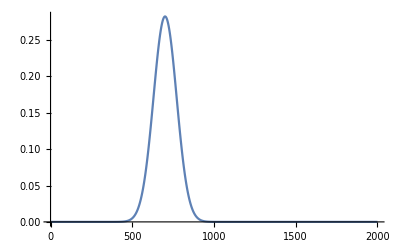

```mathematica
ListLinePlot[Map[Norm,ψ0xArray],PlotRange->All]
```

### Declaración del potencial

```mathematica
V[x_, a_, V0_] := (2V0/3) (UnitStep[x+2a] - UnitStep[x+a]) +(V0/2) (UnitStep[x+a] - UnitStep[x]) + V0 (UnitStep[x] - UnitStep[x-a]) +(V0/2) (UnitStep[x-a] - UnitStep[x - 2a])+(V0/8) (UnitStep[x-2a] - UnitStep[x-4a]);
```

```mathematica
ac = 3L;
threshold = 45;
```

```mathematica
vArray = Table[V[x, ac, V0],{x,xArray}];
Do[vArray[[i]]=10^20,{i,1,threshold}];Do[vArray[[i]]=10^20,{i,-1,-1-threshold,-1}];
```

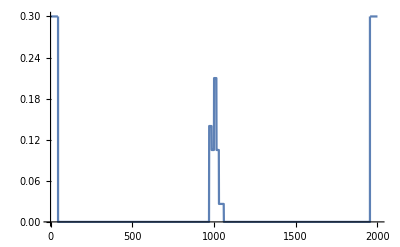

```mathematica
ListLinePlot[vArray,PlotRange->{All,{0,0.3}}]
```

### Definiciones del algoritmo

```mathematica
Stepψx[ψxArray_]:=ψxArray ⅇ^(- ⅈ/2 vArray/ℏ)Δt;
Stepψk[ψkArray_]:=ψkArray ⅇ^(- ⅈ/2 (ℏ kArray^2)/m)Δt;
Stepψ[ψxArray_]:=Block[{ψx,ψk},
ψx = ψxArray;
ψx = Stepψx[ψx];
ψk = Fourier[ψx];
ψk = Stepψk[ψk];
ψx = InverseFourier[ψk];
ψx = Stepψx[ψx];
Return[ψx];
];
```